```mathematica
AllSpectra=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/3 IA Fluorimeter and UVVis/140521 spectra.csv"];
Wavelengths=AllSpectra[[All,1]];
Insulin2={Wavelengths,AllSpectra[[All,2]]}ᵀ;
Insulin={Wavelengths,AllSpectra[[All,8]]}ᵀ;
Insulin2andPDMIAmostlyreacted={Wavelengths,AllSpectra[[All,3]]}ᵀ;
Buffer={Wavelengths,AllSpectra[[All,4]]}ᵀ;
BufferandPDMIAmostlyreacted={Wavelengths,AllSpectra[[All,6]]}ᵀ;
BufferandPDMIAunreacted={Wavelengths,AllSpectra[[All,5]]}ᵀ;
BufferandPDMIAandAminereacted={Wavelengths,AllSpectra[[All,7]]}ᵀ;
InsulinandPDMIAmostlyreacted={Wavelengths,AllSpectra[[All,10]]}ᵀ;
InsulinandPDMIAunreacted={Wavelengths,AllSpectra[[All,9]]}ᵀ;
InsulinandPDMIAveryreacted={Wavelengths,AllSpectra[[All,11]]}ᵀ;
Buffer2andPDMIAreacted={Wavelengths,AllSpectra[[All,13]]}ᵀ;
Buffer2andPDMIAunreacted={Wavelengths,AllSpectra[[All,12]]}ᵀ;
Buffer2andPDMIAandAminereacted={Wavelengths,AllSpectra[[All,14]]}ᵀ;
```

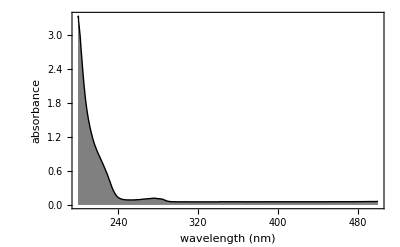

```mathematica
ListPlot[Insulin,PlotStyle->{PointSize[.01],Black},AxesOrigin->{200,0},Joined->True,Filling->Axis,FillingStyle->Gray,PlotRange->{{200,400},{0,All}},Frame->True,FrameLabel->{{"absorbance",""},{"wavelength (nm)",""}},LabelStyle->18]
```

```mathematica
Export["uvvisinsulin",%147,"PDF"]
```

uvvisinsulin

```mathematica
UVVisSpectraNames={{"Insulin","Insulin2","Insulin2andPDMIAmostlyreacted","InsulinandPDMIAmostlyreacted","InsulinandPDMIAunreacted","InsulinandPDMIAveryreacted","Buffer","BufferandPDMIAmostlyreacted","BufferandPDMIAunreacted","BufferandPDMIAandAminereacted","Buffer2andPDMIAreacted","Buffer2andPDMIAunreacted","Buffer2andPDMIAandAminereacted"},{Insulin,Insulin2,Insulin2andPDMIAmostlyreacted,InsulinandPDMIAmostlyreacted,InsulinandPDMIAunreacted,InsulinandPDMIAveryreacted,Buffer,BufferandPDMIAmostlyreacted,BufferandPDMIAunreacted,BufferandPDMIAandAminereacted,Buffer2andPDMIAreacted,Buffer2andPDMIAunreacted,Buffer2andPDMIAandAminereacted}}ᵀ;
```

```mathematica
ExportPDFSpectrum[SpectrumandName_]:=Export[StringJoin[{"uvvis",SpectrumandName[[1]],".pdf"}],MakeUVVisPlot[SpectrumandName[[2]]]]
SetAttributes[ExportPDFSpectrum,HoldFirst]
MakeUVVisPlot[spectrum_]:=ListPlot[spectrum,PlotStyle->Black,AxesOrigin->{200,0},Joined->True,Filling->Axis,FillingStyle->Gray,PlotRange->{{200,400},{0,All}},Frame->True,FrameLabel->{{"absorbance",""},{"wavelength (nm)",""}},LabelStyle->18]
```

```mathematica
ExportSpectra[spectralist_]:=Module[{index},
index=0;
While[index<Dimensions[spectralist][[1]],
index++;
ExportPDFSpectrum[spectralist[[index]]];
Print[index]]]
```

```mathematica
ExportSpectra[UVVisSpectraNames]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

```mathematica
Dimensions[UVVisSpectraNames][[1]]
```

13

```mathematica
index
```

0

```mathematica
UVVisSpectraNames
```

{Insulin,Insulin2,Insulin2andPDMIAmostlyreacted,InsulinandPDMIAmostlyreacted,InsulinandPDMIAunreacted,InsulinandPDMIAveryreacted,Buffer,BufferandPDMIAmostlyreacted,BufferandPDMIAunreacted,BufferandPDMIAandAminereacted,Buffer2andPDMIAreacted,Buffer2andPDMIAunreacted,Buffer2andPDMIAandAminereacted}